```mathematica
T = 5;
pi = {0.51,0.49}; (*indexed by group; 1 is group a, 2 is group b*) 
c = {{1,1}, {1,1}};  (*first index is group g and second is article s*)
v = {{1000, 100}, {100, 1000}}; (*first index is group g and second is article s*)
q = {0.8, 0.8}; (*indexed by group*)
F11[p_] := CDF[TruncatedDistribution[{0,1}, NormalDistribution[0.3, 0.01]], p]
F12[p_] := CDF[TruncatedDistribution[{0,1}, NormalDistribution[0.03, 0.01]], p]
F21[p_] := CDF[TruncatedDistribution[{0,1}, NormalDistribution[0.07, 0.05]], p]
F22[p_] := CDF[TruncatedDistribution[{0,1}, NormalDistribution[0.3, 0.1]], p]
eff[p_] := {{F11[p], F12[p]}, {F21[p], F22[p]}}
psi[g_,s_] := (1 - eff[c[[g]][[s]]/v[[g]][[s]]][[g]][[s]])
(*first index is group g and second is article s*)

(*model parameters just for fairness constraints; require deltalow < 1 <deltahigh *)
deltalow = 0.5;
deltahigh = 2;
```

```mathematica
(*Cell needs to be re-run with T, pi, q, F, c, or v changes*)
(*s=1 => s=a, s= 2 => s = b*)
l1[theta_, g_,s_] := Piecewise[{{pi[[g]] theta[[g]] psi[g,s], s== 1}, {pi[[g]] (1 - theta[[g]]) psi[g,s],s == 2}}, 0]
l[theta_, g_, s_, t_] := Piecewise[{{(q[[g]] l[theta, g, s, t-1] + (1 - q [[Mod[g,2] + 1]]) l[theta, Mod[g,2] + 1, s, t-1])psi[g,s] , t ≥ 2}, {l1[theta, g,s],t == 1}}, 0]
L[theta_,g_,s_] := Sum[l[theta,g,s,t], {t,1,T}]
```

```mathematica
objective[theta_] := L[theta, 1,1] + L[theta, 1,2] + L[theta, 2,1]+ L[theta, 2,2]
constraints = Reduce[deltalow ≤ L[{thetaA, thetaB}, 1,1] / L[{thetaA, thetaB}, 2,2] ≤ deltahigh && deltalow ≤ L[{thetaA, thetaB}, 1,2] / L[{thetaA, thetaB}, 2,1] ≤ deltahigh && 0 ≤ thetaA ≤ 1 && 0 ≤ thetaB ≤ 1, {thetaA,thetaB}];
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

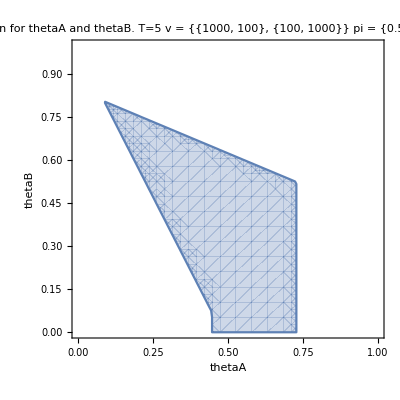

```mathematica
RegionPlot[constraints, {thetaA, 0,1}, {thetaB, 0, 1}, FrameLabel->{"thetaA", "thetaB"}, PlotLabel->("Feasible region for thetaA and thetaB.  \nT="<>ToString[T] " \n v = "<>ToString[v] "q = "<>ToString[q] " pi = "<>ToString[pi] )]
```

```mathematica
Plot3D[objective[{thetaA,thetaB}], {thetaA,0,1}, {thetaB, 0, 1}]
```

```mathematica
Maximize[{objective[{thetaA,thetaB}], 0≤ thetaA ≤ 1 && 0 ≤ thetaB ≤ 1},{thetaA,thetaB}]
```

{4.91351,{thetaA→1.,thetaB→0.}}